```mathematica
(* Notebook for analysing the magnetic vector potential of a simple wire loop and its suitability for confinement. *)
```

```mathematica
(*Initialise wire loop magnetic field using the expression computed from the Biot-Savart Law*)
ClearAll["Global`*"];
β=0.2;(* Wire loop parameter *)
a=1;(*radius of wire loop*)
g=1; (* magnitude of the current *)
B[r_]:=(g a^2)/(4π)NIntegrate[(a^2-r a Cos[ϕ])/((r^2+(β a)^2+a^2-2 a r Cos[ϕ])^(3/2)),{ϕ,0,2π}];
(*Plot3D[B[Sqrt[x^2+y^2]],{x,-2a,2a},{y,-2a,2a},AxesLabel->{x,y,"B(r)"},ColorFunction->"ThermometerColors",PlotLegends->Automatic,LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],Boxed->False,ImageSize->Full]*)
```

```mathematica
(*Derive the magnetic vector potential by applying the relevant components of the curl operator and solve.*)
s=NDSolve[{D[V[r],r]+V[r]/r==B[r],V[0.001]==0},V,{r,0.001,10a}];
V=First[V/.s];
```

NIntegrate::inumr: The integrand (1-r Cos[ϕ])/((1.04+r^2-2 r Cos[ϕ])^(3/2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NDSolve::nbnum1: The function value -0.002 Im[Cos[ϕ]]==0 is not True or False when the arguments are {0.001,0.,0.471433}.

NDSolve::nbnum1: The function value 1.04-0.002 Re[Cos[ϕ]]≤0 is not True or False when the arguments are {0.001,0.,0.471433}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at r = 0.001 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at r = 0.00100002 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at r = 0.00100005 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

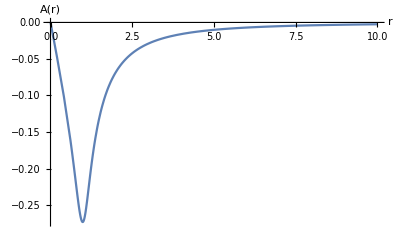

```mathematica
(*Plot the magnetic vector potential*)
Plot[-V[r],{r,0.001,10a},AxesLabel->{"r","A(r)"},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->{{0,5.2},{0.01,-0.30}}]
```

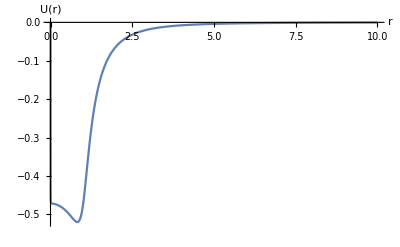

```mathematica
m=1; (*magnetic quantum number under investigation*)
U[r_]:=(V[r])^2-(2m)/r(V[r]); (*Find effective scalar potential of the vector potential*)
Plot[U[r],{r,0.001,10a},AxesLabel->{"r","U(r)"},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->All]
```

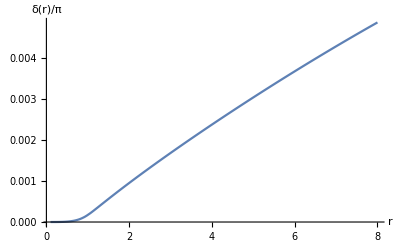

```mathematica
k=0.1;
iterations=100;
For[i=0,i<iterations,i++,
Subscript[δ, temp]=NDSolveValue[{δ'[r]==-π/2 r(U[r])(BesselJ[m,k r]Cos[δ[r]]-BesselY[m,k r]Sin[δ[r]])^2,δ[0.1]==0},δ,{r,0.1,10}];
δ[r]=Subscript[δ, temp][r];]
Plot[δ[r]/π,{r,0.1,8},AxesLabel->{r,"δ(r)/π"}, LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->All]
```